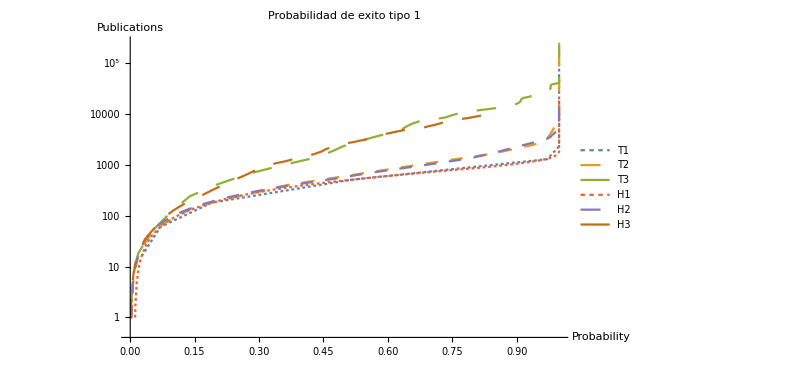
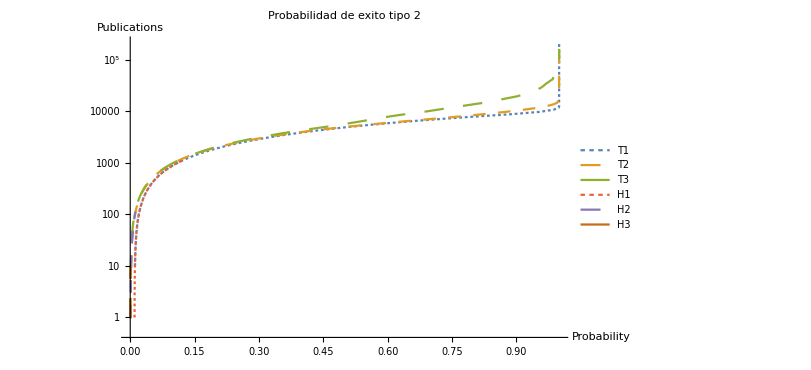
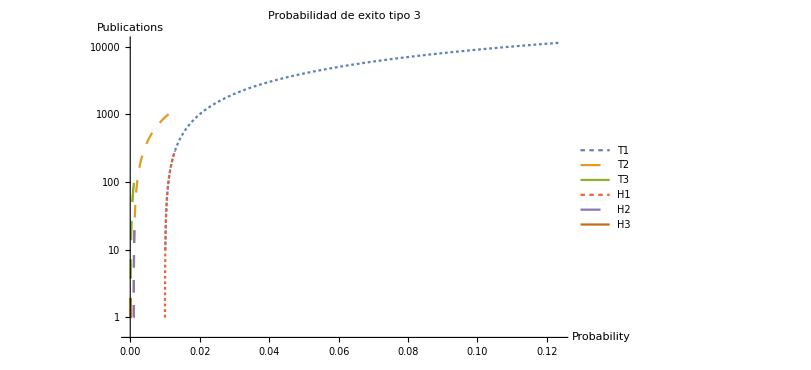
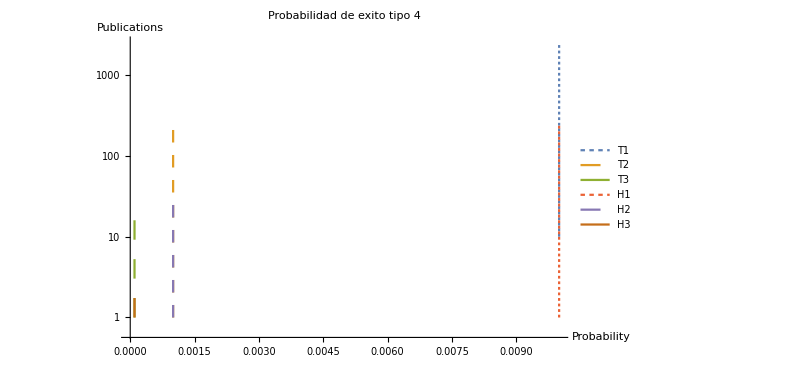
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados/SinCompetencia";
SetDirectory[y<>"/images"];
SetOptions[ListLogPlot,BaseStyle->{FontSize->18}];
pub1= Import[y<>"/averageResults/prob-pub-1-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/prob-pub-1-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/prob-pub-1-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/prob-pub-5-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/prob-pub-5-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/prob-pub-5-1.0E-4-curve.csv"];
plotPub1= Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Probability","Publications"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 1",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];

Export["prob-pub-1.png",plotPub1];

pub1= Import[y<>"/averageResults/prob-pub-2-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/prob-pub-2-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/prob-pub-2-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/prob-pub-6-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/prob-pub-6-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/prob-pub-6-1.0E-4-curve.csv"];
plotPub2 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Probability","Publications"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 2", PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["prob-pub-2.png",plotPub2];

pub1= Import[y<>"/averageResults/prob-pub-3-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/prob-pub-3-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/prob-pub-3-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/prob-pub-7-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/prob-pub-7-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/prob-pub-7-1.0E-4-curve.csv"];
plotPub3 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Probability","Publications"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All,PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 3",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["prob-pub-3.png",plotPub3];

pub1= Import[y<>"/averageResults/prob-pub-4-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/prob-pub-4-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/prob-pub-4-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/prob-pub-8-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/prob-pub-8-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/prob-pub-8-1.0E-4-curve.csv"];
plotPub4 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Probability","Publications"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All, PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 4",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["prob-pub-4.png",plotPub4];

pubTotal=Grid[{{plotPub1,plotPub2},{plotPub3,plotPub4}}]
Export["prob-pub-total-100-true.png",pubTotal];
```